```mathematica
R0=0.;
D0 =5.;
R1=7.;
D1=3.;
L=(R1+D1)/2;
Np=10000;
r1=RandomReal[{R0,R0+D0}, Np];
r2 = RandomReal[{R1,R1+D1}, Np];
alpha = RandomReal[{0, 2Pi}, Np];
```

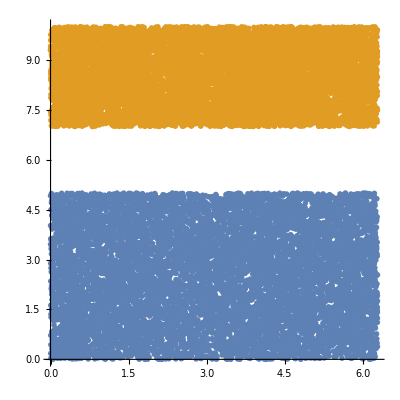

```mathematica
a = Transpose[{alpha,r1}];
b = Transpose[{alpha,r2}];
ListPlot[{a,b}, PlotStyle->{PointSize->0.01}, AspectRatio->1]
```

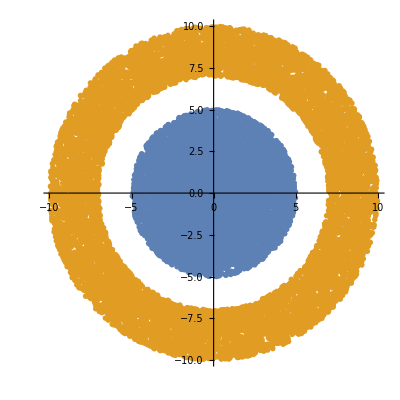

```mathematica
c=Map[{#[[2]] Cos[#[[1]]], #[[2]] Sin[#[[1]]]}&, a];
d=Map[{#[[2]] Cos[#[[1]]], #[[2]] Sin[#[[1]]]}&, b];
ListPlot[{c,d}, PlotStyle->{PointSize->0.01}, AspectRatio->1]
```

```mathematica
e=Map[L{+(#[[2]]-R0)/D0 Sign[#[[1]]-Pi],#[[1]]/Pi}&, a];
f=Map[L{-(#[[2]]-R1)/D1 Sign[#[[1]]-Pi],#[[1]]/Pi}&,b];
ListPlot[{e,f}, PlotStyle->{PointSize->0.01}, AspectRatio->1]
```